```mathematica
Vsupply=20; (* supply voltage *)
Rfet=5 10^-3; (* minimum on resistance of a single FET *)
Nfets=5; (* number of current controlling fets in parallel *)
Rcoils=0.1; (* resistance of coil pair *)
Imax=Vsupply/(Rcoils+Rfet/Nfets);

Vfets[II_]:=Vsupply - II*Rcoils;
Pfet[II_]:=II*Vfets[II]/Nfets;
```

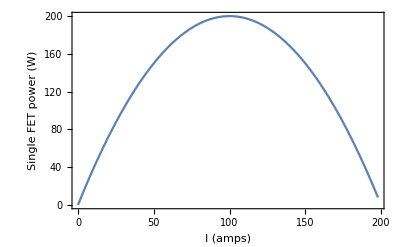

```mathematica
Plot[Pfet[i],{i,0,Imax},Axes->False,Frame->True,LabelStyle->{Black,Medium},FrameStyle->Black,FrameLabel->{"I (amps)","Single FET power (W)"}]
```

```mathematica
II[t_]:=t*100; (* 100 A/s ramp rate *)
NIntegrate[Pfet[II[t]],{t,0,1}]
```

133.333